```mathematica
Table[Integrate[Exp[-y^2/(2*z^2)],{y,z^2/2,Infinity}],{z,1,0.01,-0.01}]
```

{0.773389,0.770029,0.766591,0.763075,0.759481,0.755808,0.752056,0.748224,0.744312,0.740319,0.736246,0.732092,0.727855,0.723537,0.719137,0.714654,0.710087,0.705438,0.700704,0.695886,0.690984,0.685996,0.680924,0.675765,0.670521,0.665191,0.659773,0.654269,0.648678,0.642999,0.637231,0.631376,0.625432,0.619399,0.613277,0.607065,0.600763,0.594371,0.587889,0.581316,0.574652,0.567897,0.56105,0.554112,0.547081,0.539958,0.532742,0.525433,0.518031,0.510536,0.502947,0.495264,0.487487,0.479616,0.47165,0.463589,0.455433,0.447182,0.438836,0.430394,0.421856,0.413222,0.404491,0.395665,0.386741,0.377721,0.368604,0.35939,0.350078,0.340669,0.331162,0.321558,0.311856,0.302055,0.292157,0.28216,0.272064,0.26187,0.251578,0.241186,0.230696,0.220107,0.209418,0.198631,0.187744,0.176758,0.165672,0.154487,0.143202,0.131818,0.120333,0.10875,0.097066,0.0852825,0.0733991,0.0614158,0.0493326,0.0371494,0.0248663,0.0124831}

```mathematica
Table[Integrate[(Exp[log-z^2/2+y]-1)*1/z*Exp[-y^2/(2*z^2)],{y,z^2/2-log,Infinity}],{z,1,0,-0.1},{log,0.1,0,-0.02}]//MatrixForm
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

(1.14677-6.52957×10^-16 ⅈ | 1.10714-6.40027×10^-16 ⅈ | 1.06866-6.27354×10^-16 ⅈ | 1.03131-6.14931×10^-16 ⅈ | 0.995042-6.02755×10^-16 ⅈ | 0.95985-5.9082×10^-16 ⅈ
1.05339-5.82278×10^-16 ⅈ | 1.01451-5.70748×10^-16 ⅈ | 0.976804-5.59447×10^-16 ⅈ | 0.940257-5.48369×10^-16 ⅈ | 0.90484-5.3751×10^-16 ⅈ | 0.870526-5.26867×10^-16 ⅈ
0.958013-5.17135×10^-16 ⅈ | 0.919842-5.06895×10^-16 ⅈ | 0.8829-4.96858×10^-16 ⅈ | 0.847159-4.87019×10^-16 ⅈ | 0.812591-4.77375×10^-16 ⅈ | 0.779169-4.67923×10^-16 ⅈ
0.860904-4.57338×10^-16 ⅈ | 0.823389-4.48282×10^-16 ⅈ | 0.787168-4.39405×10^-16 ⅈ | 0.75221-4.30704×10^-16 ⅈ | 0.718486-4.22176×10^-16 ⅈ | 0.685967-4.13816×10^-16 ⅈ
0.762374-4.02683×10^-16 ⅈ | 0.725421-3.94709×10^-16 ⅈ | 0.68985-3.86893×10^-16 ⅈ | 0.655631-3.79232×10^-16 ⅈ | 0.622731-3.71723×10^-16 ⅈ | 0.59112-3.64362×10^-16 ⅈ
0.662831-3.52951×10^-16 ⅈ | 0.626275-3.45962×10^-16 ⅈ | 0.591232-3.39111×10^-16 ⅈ | 0.557668-3.32397×10^-16 ⅈ | 0.525549-3.25815×10^-16 ⅈ | 0.49484-3.19363×10^-16 ⅈ
0.562873-3.0791×10^-16 ⅈ | 0.526417-3.01813×10^-16 ⅈ | 0.491672-2.95836×10^-16 ⅈ | 0.458604-2.89978×10^-16 ⅈ | 0.427176-2.84237×10^-16 ⅈ | 0.397349-2.78608×10^-16 ⅈ
0.463578-2.67315×10^-16 ⅈ | 0.426625-2.62022×10^-16 ⅈ | 0.391714-2.56833×10^-16 ⅈ | 0.358812-2.51748×10^-16 ⅈ | 0.327882-2.46763×10^-16 ⅈ | 0.298879-2.41877×10^-16 ⅈ
0.367604-2.30912×10^-16 ⅈ | 0.328722-2.2634×10^-16 ⅈ | 0.292501-2.21858×10^-16 ⅈ | 0.258937-2.17465×10^-16 ⅈ | 0.228007-2.13159×10^-16 ⅈ | 0.199667-2.08938×10^-16 ⅈ
0.285562-1.98439×10^-16 ⅈ | 0.240108-1.9451×10^-16 ⅈ | 0.19854-1.90658×10^-16 ⅈ | 0.161191-1.86883×10^-16 ⅈ | 0.128298-1.83183×10^-16 ⅈ | 0.0999583-1.79555×10^-16 ⅈ
ComplexInfinity | ComplexInfinity | ComplexInfinity | ComplexInfinity | ComplexInfinity | ComplexInfinity)

```mathematica
With[{z=x+I y}, Re[z]]
```

-Im[y]+Re[x]

```mathematica
Expand[Cos[x+I y]]
```

Cos[x+ⅈ y]

```mathematica
ComplexExpand[Cos[x+I y]]
```

Cos[x] Cosh[y]-ⅈ Sin[x] Sinh[y]

```mathematica
Re[Cos[x+ I y]]
```

Re[Cos[x+ⅈ y]]

```mathematica
ComplexExpand[Re[Cos[x+I y]]]
```

Cos[x] Cosh[y]

```mathematica
RE[z_]:=ComplexExpand[Re[z]];
IM[z_]:=ComplexExpand[Im[z]];
OrthogonalTrajectores[u_,v_,b]:=
	Show[ContourPlot[u[x,y],{x,-b,b},{y,-b,b},Contours->30,ContourStyle->{{Thick,Red}},
		PlotPoints->30,ContourShading->False],
		ContourPlot[v[x,y],{x,-b,b},{y,-b,b},Contours->30,ContourStyle->{{Thick,Blue}},
		PlotPoints->30,ContourShading->False]];
PtoC[{x_,y_}]:=x+I y;
CtoP[z_]:={RE[x],IM[y]};
```

```mathematica
f[z_]:=1/(1+z^2);
u[{x_,y_}]:=RE[f[x+I y]];
v[{x_,y_}]:=IM[f[x+I y]];
Φ[{x_,y_}]:={u[{x,y}],v[{x,y}]};
Φ̄[{x_,y_}]:={u[{x,y}],-v[{x,y}]};
SuperStar[Φ][{x_,y_}]:={v[{x,y}],u[{x,y}]};
Subscript[x, z0_,R_][t_]:=Re[z0]+R*Cos[t];
Subscript[y, z0_,R_][t_]:=Re[Z0]+R*Sin[t];
Subscript[z, z0_,R_][t_]:=Subscript[x, z0,R][t]+I*Subscript[y, z0,R][t];
Subscript[r, z0_,R_][t_]:={Subscript[x, z0,R][t],Subscript[y, z0,R][t]};
```

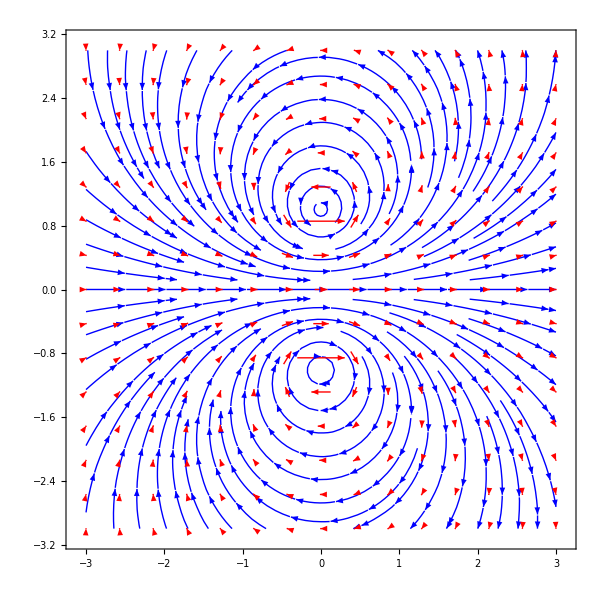

```mathematica
Show[StreamPlot[Φ̄[{x,y}],{x,-3,3},{y,-3,3},StreamStyle->Blue],
	VectorPlot[Φ̄[{x,y}],{x,-3,3},{y,-3,3},VectorStyle->Red],
	ParametricPlot[Subscript[r, PtoC[{1,1}],.5][t],{t,0,2*Pi},PlotStyle->{Thick,Green}],ImageSize->600]
```

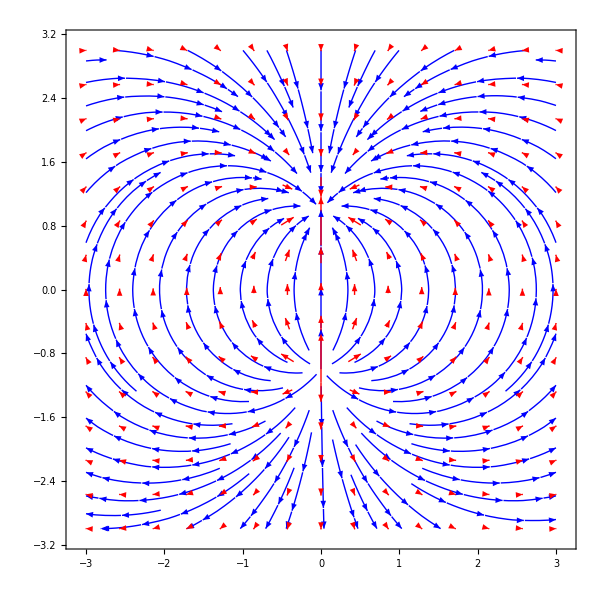

```mathematica
Show[StreamPlot[SuperStar[Φ][{x,y}],{x,-3,3},{y,-3,3},StreamStyle->Blue],
	VectorPlot[SuperStar[Φ][{x,y}],{x,-3,3},{y,-3,3},VectorStyle->Red],
	ParametricPlot[Subscript[r, PtoC[{1,1}],.5][t],{t,0,2 Pi},PlotStyle->{Thick,Green}],ImageSize->600]
```

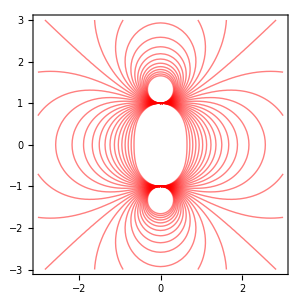
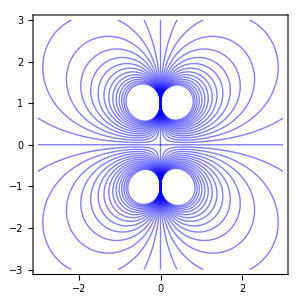

```mathematica
Show[ContourPlot[u[{x,y}],{x,-3,3},{y,-3,3},Contours->30,ContourStyle->{{Thick,Red}},
		PlotPoints->30,ContourShading->False],ImageSize->300]Show[ContourPlot[v[{x,y}],{x,-3,3},{y,-3,3},Contours->30,ContourStyle->{{Thick,Blue}},
		PlotPoints->30,ContourShading->False],ImageSize->300]
```

```mathematica
f[z_]:=1/(1+z^.5);
Subscript[u, f_][{x_,y_}]:=RE[f[x+I y]];
Subscript[v, f_][{x_,y_}]:=IM[f[x+I y]];
Subscript[Φ, f_][{x_,y_}]:={Subscript[u, f][{x,y}],Subscript[v, f][{x,y}]};
Subscript[Φ̄, f_][{x_,y_}]:={Subscript[u, f][{x,y}],-Subscript[v, f][{x,y}]};
SuperStar[Subscript[Φ, f_]][{x_,y_}]:={Subscript[v, f][{x,y}],Subscript[u, f][{x,y}]};
```

```mathematica
f[z_]:=NIntegrate[1/z*Exp[y^2/(z^2)],{y,z^2/2,10}];
u[{x_,y_}]:=RE[f[x+I y]];
v[{x_,y_}]:=IM[f[x+I y]];
Φ[{x_,y_}]:={u[{x,y}],v[{x,y}]};
Φ̄[{x_,y_}]:={u[{x,y}],-v[{x,y}]};
SuperStar[Φ][{x_,y_}]:={v[{x,y}],u[{x,y}]};
Show[StreamPlot[Φ̄[{x,y}],{x,-3,3},{y,-3,3},StreamStyle->Blue],
VectorPlot[Φ̄[{x,y}],{x,-3,3},{y,-3,3},VectorStyle->Red],
	ParametricPlot[Subscript[r, PtoC[{1,1}],.5][t],{t,0,2*Pi},PlotStyle->{Thick,Green}],ImageSize->600]
```

NIntegrate::nlim: y = 1/2 (x+ⅈ y)^2 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[StreamPlot[Φ̄[{x,y}],{x,-3,3},{y,-3,3},StreamStyle→Blue],VectorPlot[Φ̄[{x,y}],{x,-3,3},{y,-3,3},VectorStyle→Red],,ImageSize→600].

Show[StreamPlot[Φ̄[{x,y}],{x,-3,3},{y,-3,3},StreamStyle→Blue],VectorPlot[Φ̄[{x,y}],{x,-3,3},{y,-3,3},VectorStyle→Red],-Graphics-,ImageSize→600]

```mathematica
ComplexExpand[Re[Exp[I (x+I y)-(x+I y)^2/2]]]
ComplexExpand[Im[Exp[I (x+I y)-(x+I y)^2/2]]]
```

ⅇ^(-y+1/2 (-x^2+y^2)) Cos[x-x y]

ⅇ^(-y+1/2 (-x^2+y^2)) Sin[x-x y]

```mathematica
ComplexExpand[Exp[x+I y]]
```

ⅇ^x Cos[y]+ⅈ ⅇ^x Sin[y]

```mathematica
ContourPlot[Exp[x+I y],{x,y}]
```

ContourPlot::pllim: Range specification {x,y} is not of the form {x, xmin, xmax}.

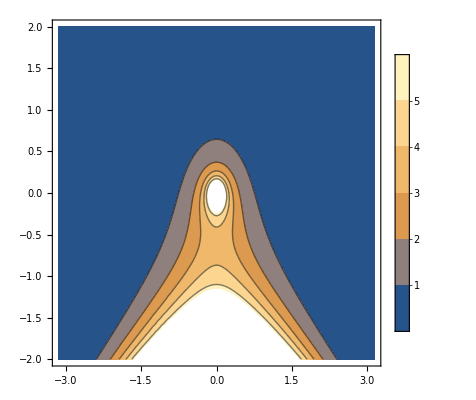

```mathematica
ContourPlot[
Abs[Exp[I (x+I y)-(x+I y)^2/2]/(I(x+I y))],{x,-Pi,Pi},{y,-2,2},PlotLegends->Automatic]
```

```mathematica
Plot3D[Abs[Exp[ⅈ (x+ⅈ y)-1/2 (x+ⅈ y)^2]/(ⅈ (x+ⅈ y))],{x,-5,5},{y,-3,6},PlotPoints->100,MaxRecursion->9,Mesh->Automatic,MeshFunctions->{#3&},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
lewis[x_,y_]:=Module[{a=(2 I)/(2 Pi)},
Exp[ⅈ (x+ⅈ y-a )-1/2 (x+ⅈ y)^2]((- I)/(2 Pi)) Exp[2 Pi x I] (1/(x + I y+a)-1/(x+I y +a-I/(2 Pi)))]
```

```mathematica
Plot3D[Abs[lewis[x,y]]//Log,{x,-5,5},{y,-3,6},PlotPoints->100,Mesh->Automatic,MeshFunctions->{#3&},PlotLegends->Automatic,ImageSize->Large]
```

-Graphics3D-